## Importing the Imagenette Dataset

```mathematica
trainDirectory = "/home/mk/imagenette2-160/train/";
testDirectory  = "/home/mk/imagenette2-160/val/";
form = "*.JPEG";

ImportLabeldFilePaths[parentDirectory_,form_]:= Module[{paths,ExtractLabelFromFilePath,LabeledFilePath},
paths = FileNames[form,parentDirectory,2];
ExtractLabelFromFilePath[path_] := Part[FileNameSplit[path],-2];
LabeledFilePath[path_] := File[path]->ExtractLabelFromFilePath[path] ;
Return[Map[LabeledFilePath,paths]]
]
```

```mathematica
trainingDataFiles = ImportLabeldFilePaths[trainDirectory,form];
testDataFiles = ImportLabeldFilePaths[testDirectory,form];
labels = Union[trainingDataFiles[[All,2]]];
labels
```

{n01440764,n02102040,n02979186,n03000684,n03028079,n03394916,n03417042,n03425413,n03445777,n03888257}

```mathematica
Length[trainingDataFiles]
```

9469

```mathematica
Length[testDataFiles]
```

3925

```mathematica
genTrain=Function[RandomSample[trainingDataFiles,#BatchSize]]
```

RandomSample[trainingDataFiles,#BatchSize]&

```mathematica
(Import[#[[1]]]->#[[2]])& /@ genTrain[<|"BatchSize"->4|>]
```

{-Graphics-→n01440764,-Graphics-→n03417042,-Graphics-→n03888257,-Graphics-→n03888257}

## VGGNet

uniform architecture

Grouping multiple convolutions into blocks

Progressively double the number of filters across blocks

Progressively half  the input dimension(width and height) across blocks through pooling layers at the end of each block

All convolutional layers in a block  have the same kernel size, stride = 1, number of filter, padding = “same”

```mathematica
activation = Ramp;
kfilter = 3;
kpooling = 2;
nfilters = 64;
imageEnc  = NetEncoder[{"Image",{224,224},ColorSpace->"RGB"}]
```

NetEncoder[<>]

```mathematica
block1 = NetChain[{
ConvolutionLayer[nfilters,kfilter,"PaddingSize"->"Same"],activation,
ConvolutionLayer[nfilters,kfilter,"PaddingSize"->"Same"],activation,
PoolingLayer[kpooling,"Stride"->2]
}];

block2 = NetChain[{
ConvolutionLayer[2*nfilters,kfilter,"PaddingSize"->"Same"],activation,
ConvolutionLayer[2*nfilters,kfilter,"PaddingSize"->"Same"],activation,
PoolingLayer[kpooling,"Stride"->2]
}];

block3 = NetChain[{
ConvolutionLayer[4*nfilters,kfilter,"PaddingSize"->"Same"],activation,
ConvolutionLayer[4*nfilters,kfilter,"PaddingSize"->"Same"],activation,
ConvolutionLayer[4*nfilters,kfilter,"PaddingSize"->"Same"],activation,
PoolingLayer[kpooling,"Stride"->2]
}];

block4 = NetChain[{
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,
PoolingLayer[kpooling,"Stride"->2]
}];


block5 = NetChain[{
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,
PoolingLayer[kpooling,"Stride"->2]
}];

classifier = NetChain[{LinearLayer[4096],activation,LinearLayer[4096],activation,LinearLayer[1000],SoftmaxLayer[]}];

classDec = NetDecoder[{"Class",Range[1,1000]}];
```

```mathematica
VGGNet = NetChain[<|"block1"-> block1,"block2"->block2,"block3"->block3,"block4"->block4,"block5"->block5,"flatten"->FlattenLayer[],"classifier"->classifier|>,"Input"->imageEnc,"Output"->classDec]
```

NetChain[<>]

```mathematica
Information[VGGNet]
```

Net Information

## miniVGGNet

```mathematica
activation = Ramp;
kfilter = 3;
kpooling = 2;
nfilters = 16;
imageEnc  = NetEncoder[{"Image",{120,120},ColorSpace->"RGB"}]
```

NetEncoder[<>]

```mathematica
block1 = NetChain[{
ConvolutionLayer[nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
ConvolutionLayer[nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
PoolingLayer[kpooling,"Stride"->2]
}];

block2 = NetChain[{
ConvolutionLayer[2*nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
ConvolutionLayer[2*nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
PoolingLayer[kpooling,"Stride"->2]
}];

block3 = NetChain[{
ConvolutionLayer[4*nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
ConvolutionLayer[4*nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
ConvolutionLayer[4*nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
PoolingLayer[kpooling,"Stride"->2]
}];

block4 = NetChain[{
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
PoolingLayer[kpooling,"Stride"->2]
}];


block5 = NetChain[{
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
ConvolutionLayer[8*nfilters,kfilter,"PaddingSize"->"Same"],activation,BatchNormalizationLayer[],
PoolingLayer[kpooling,"Stride"->2]
}];

classifier = NetChain[{LinearLayer[200],activation,LinearLayer[200],activation,LinearLayer[10],SoftmaxLayer[]}];

classDec = NetDecoder[{"Class",labels}];
```

```mathematica
miniVGGNet = NetChain[<|"block1"-> block1,"block2"->block2,"block3"->block3,"block4"->block4,"block5"->block5,"flatten"->FlattenLayer[],"classifier"->classifier|>,"Input"->imageEnc,"Output"->classDec]
```

NetChain[<>]

```mathematica
Information[miniVGGNet]
```

Net Information

## Training

```mathematica
miniVGGNet = NetTrain[miniVGGNet,{genTrain,"RoundLength"->Length[trainingDataFiles]},BatchSize->32,MaxTrainingRounds->50,ValidationSet->Scaled[0.1]]
```

NetChain[<>]

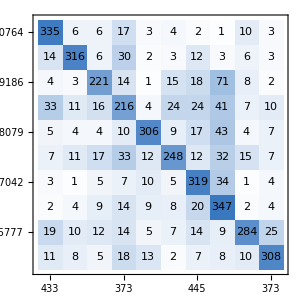
{0.738854,0.144204,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[miniVGGNet,testDataFiles,{"Accuracy","ErrorRate"->2,"ConfusionMatrixPlot"}]
```